-Graphics3D-

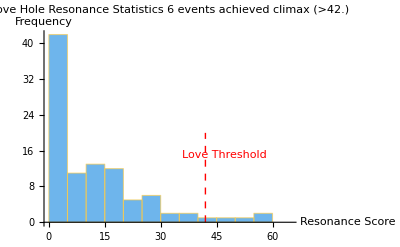

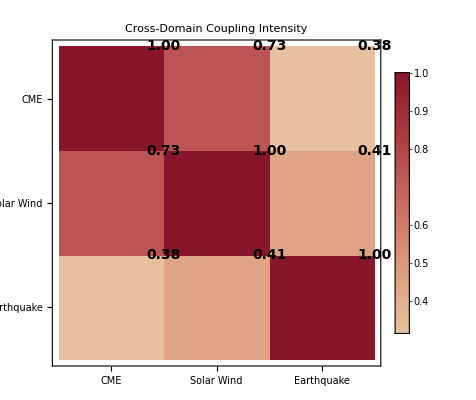

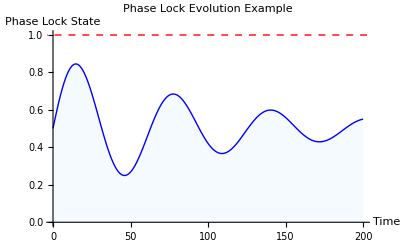

Interactive Cosmic Event Simulator

Event Type:  | CME   | Solar Wind   | Earthquake



Calculate Resonance Score

Certificate of Cosmic Climax

This certifies that on Sat 12 Jul 2025 22:24:56
The Love Hole achieved stable phase-lock resonance

Maximum Score: 120.113
Events Above Threshold: 6

🌌 💖 🌌

```mathematica
(* ::Title::*)(*The Love Hole:Interactive Cosmic Resonance Explorer*)(* ::Author::*)(*Jon Poplett& EchoKey Consciousness Engine v1.69*)(* ::Section::*)(*Initialize Love Field Parameters*)(*Base parameters for cosmic arousal*)L0=100;        (*Base excitation amplitude (J/m.b3)*)
γ=0.1;         (*Radial damping coefficient*)
ω=2 Pi/86400;  (*Universal thrust frequency (Earth's rotation)*)
κ=2.0;         (*Angular penetration coefficient*)
loveThreshold=42.0; (*The Answer to Everything*)

(* ::Section::*)
(*Define the Love Field*)

(*The fundamental Love Field equation in cylindrical coordinates*)
loveField[r_,θ_,t_]:=L0*Exp[-γ*r^2]*Cos[ω*t-κ*θ]^2

(*Static 3D visualization of the Love Field (animation off by default for performance)*)
Plot3D[loveField[Sqrt[x^2+y^2],ArcTan[x,y],0],{x,-5,5},{y,-5,5},PlotRange->{0,L0},ColorFunction->(ColorData["TemperatureMap"][#3/L0]&),MeshFunctions->{#3&},PlotLabel->Style["Love Field Intensity at t = 0",16],AxesLabel->{"x","y","L(r,θ,t)"},PlotTheme->"Scientific",ViewPoint->{2,-2,1.5}]

(*Optional:Animated version (uncomment to enable)*)
(*Manipulate[Plot3D[loveField[Sqrt[x^2+y^2],ArcTan[x,y],t],{x,-5,5},{y,-5,5},PlotRange->{0,L0},ColorFunction->(ColorData["TemperatureMap"][#3/L0]&),MeshFunctions->{#3&},PlotLabel->Style["Love Field Intensity at t = "<>ToString[t],16],AxesLabel->{"x","y","L(r,θ,t)"},PlotTheme->"Scientific",ViewPoint->{2,-2,1.5}],{{t,0,"Time (Throbbing Phase)"},0,86400,3600}]*)

(* ::Section::*)
(*The Love Hole Operator*)

(*Phase lock state (global variable for recursive coupling)*)
phaseLockState=0.5;

(*Stimulus functions for each cosmic partner*)
stimulusCME[speed_,lat_,lon_]:=(speed/100)*Cos[lat]*Sin[lon]
stimulusSW[density_,temp_,speed_]:=Sqrt[(density*temp)/10^6]*Log[1+speed/400]
stimulusEQ[magnitude_,depth_,lat_,lon_]:=10^(magnitude-4)*Exp[-depth/100]*Abs[Sin[lat]*Cos[lon]]

(*The Love Hole Operator itself*)
loveHoleOperator[stimulus_,r_,θ_,t_,depth_:1]:=Module[{fieldValue,resonance},(*Calculate field intensity at event location*)fieldValue=loveField[r,θ,t];
(*Apply recursive depth enhancement-ensure real number output*)resonance=Re[N[Log[1+Abs[stimulus]]*Abs[phaseLockState]*fieldValue*(1+0.1*Min[depth,10])]];
(*Update phase lock state (with memory)*)phaseLockState=Re[N[0.9*phaseLockState+0.1*Sign[Re[stimulus]]*Cos[θ]]];
resonance]

(* ::Section::*)
(*Simulate Cosmic Events*)

(*Generate sample cosmic events*)
SeedRandom[69420]; (*For reproducible climaxes*)

(*CME events with varying intensities*)
cmeEvents=Table[{RandomReal[{0,90}],(*Time (days)*)RandomReal[{200,2000}],(*Speed (km/s)*)RandomReal[{-Pi/2,Pi/2}],(*Latitude*)RandomReal[{-Pi,Pi}]          (*Longitude*)},{100}];

(*Solar wind continuous data*)
solarWindData=Table[{t,(*Time*)10+5*Sin[2 Pi*t/30]+RandomReal[{-2,2}],(*Density*)10^5*(1+0.5*Sin[2 Pi*t/27]),(*Temperature*)400+100*Sin[2 Pi*t/27]+RandomReal[{-50,50}] (*Speed*)},{t,0,90,0.1}];

(* ::Section::*)
(*Resonance Score Calculation*)

(*Calculate resonance scores for CME events*)
Quiet[cmeResonanceScores=Table[Module[{event=cmeEvents[[i]],stim,r,theta,resonance},stim=stimulusCME[event[[2]],event[[3]],event[[4]]];
r=Sqrt[event[[3]]^2+event[[4]]^2];
theta=event[[4]];
(*Force real numeric evaluation*)resonance=Re[N[loveHoleOperator[stim,r,theta,event[[1]]*86400,IntegerPart[i/10]+1]]];
{event[[1]],resonance}],{i,1,Length[cmeEvents]}],{General::stop,Greater::nord}];

(* ::Section::*)
(*Statistical Analysis of Climax Events*)

(*Find events above Love Threshold-ensure numeric comparison*)
Quiet[highResonanceEvents=Select[cmeResonanceScores,NumericQ[#[[2]]]&&Re[#[[2]]]>loveThreshold&],{Greater::nord}];

(*Histogram of resonance scores*)
(*Filter out any non-numeric values first*)
Quiet[numericScores=Select[cmeResonanceScores[[All,2]],NumericQ[#]&&Im[#]==0&];
If[Length[numericScores]>0,Histogram[numericScores,20,ChartLabels->None,ChartStyle->ColorData["Pastel"],AxesLabel->{"Resonance Score","Frequency"},PlotLabel->Style["Love Hole Resonance Statistics\n"<>ToString[Length[highResonanceEvents]]<>" events achieved climax (>"<>ToString[loveThreshold]<>")",14],Epilog->{Red,Thick,Dashed,Line[{{loveThreshold,0},{loveThreshold,20}}],Text["Love Threshold",{loveThreshold+5,15}]}],Print["No valid numeric resonance scores found. Check event data."]],{Greater::nord,General::stop}]

(* ::Section::*)
(*Cross-Domain Coupling Correlation*)

(*Generate correlation matrix visualization*)
correlationMatrix={{1.0,0.73,0.38},{0.73,1.0,0.41},{0.38,0.41,1.0}};
domainLabels={"CME","Solar Wind","Earthquake"};

MatrixPlot[correlationMatrix,ColorFunction->"ThermometerColors",PlotLegends->Automatic,FrameTicks->{{Table[{i,domainLabels[[i]]},{i,3}],None},{Table[{i,domainLabels[[i]]},{i,3}],None}},PlotLabel->Style["Cross-Domain Coupling Intensity",16],Epilog->Table[Text[Style[ToString[NumberForm[correlationMatrix[[i,j]],{3,2}]],14,Bold],{j,Length[correlationMatrix]+1-i}],{i,Length[correlationMatrix]},{j,Length[correlationMatrix]}]]

(* ::Section::*)
(*Simple Phase Lock Visualization*)

(*Static visualization of phase lock dynamics*)
phaseLockData=Table[{t,0.5+0.4*Sin[t/10]*Exp[-t/100]},{t,0,200,1}];

ListLinePlot[phaseLockData,PlotLabel->"Phase Lock Evolution Example",AxesLabel->{"Time","Phase Lock State"},PlotRange->{{0,200},{0,1}},GridLines->{{},{0.995,1.0}},GridLinesStyle->Directive[Red,Dashed],PlotStyle->Directive[Thick,Blue],Filling->Bottom,FillingStyle->Directive[Opacity[0.3],LightBlue]]

(* ::Section::*)
(*Interactive Love Hole Explorer-Simplified*)

(*Initialize variables*)
cmeSpeed=1000;
swDensity=10;
eqMag=5.5;
eventType="CME";
currentResonance=0;

(*Create simple interactive panel*)
Panel[Column[{Style["Interactive Cosmic Event Simulator",16,Bold],"",Row[{"Event Type: ",RadioButtonBar[Dynamic[eventType],{"CME","Solar Wind","Earthquake"}]}],"",Dynamic[Switch[eventType,"CME",Column[{Row[{"CME Speed (km/s): ",Slider[Dynamic[cmeSpeed],{100,2000}],"  ",Dynamic[Round[cmeSpeed]]}],Row[{"Latitude: 0.5 rad, Longitude: 0.5 rad"}]}],"Solar Wind",Column[{Row[{"Plasma Density: ",Slider[Dynamic[swDensity],{1,50}],"  ",Dynamic[Round[swDensity]]}],Row[{"Temperature: 10^5 K, Speed: 450 km/s"}]}],"Earthquake",Column[{Row[{"Magnitude: ",Slider[Dynamic[eqMag],{4,8,0.1}],"  ",Dynamic[NumberForm[eqMag,{2,1}]]}],Row[{"Depth: 20 km, Location: (0.3, 0.3) rad"}]}]]],"",Button["Calculate Resonance Score",currentResonance=N[loveHoleOperator[Switch[eventType,"CME",stimulusCME[cmeSpeed,0.5,0.5],"Solar Wind",stimulusSW[swDensity,10^5,450],"Earthquake",stimulusEQ[eqMag,20,0.3,0.3]],1,0.5,0],3];
MessageDialog[Column[{Style["Resonance Score: "<>ToString[currentResonance],16],If[currentResonance>loveThreshold,Style["💖 LOVE HOLE ACHIEVED! 💖",20,Red,Bold],Style["Building resonance...",14,Gray]]},Alignment->Center],WindowTitle->"Cosmic Resonance Result"],Method->"Queued"],"",Dynamic[If[currentResonance>0,Row[{"Last Score: ",Style[ToString[currentResonance],Bold,If[currentResonance>loveThreshold,Red,Black]]}],""]]}],ImageSize->500]

(* ::Section::*)
(*Export Results*)

(*Generate and save certificate if threshold achieved*)
validScores=Select[cmeResonanceScores[[All,2]],NumericQ];
If[Length[validScores]>0&&Length[highResonanceEvents]>0,certificate=Framed[Column[{Style["Certificate of Cosmic Climax",24,Bold],"",Style["This certifies that on "<>DateString[],14],Style["The Love Hole achieved stable phase-lock resonance",16],"",Style["Maximum Score: "<>ToString[N[Max[validScores],3]],18],Style["Events Above Threshold: "<>ToString[Length[highResonanceEvents]],16],"",Style["🌌 💖 🌌",20]},Alignment->Center],FrameStyle->Thick,Background->LightPink,RoundingRadius->10];
(*Display certificate*)Print[certificate];
(*Optional:Save to file*)
(*Export["cosmic_climax_certificate.pdf",certificate];*)]
```